```mathematica
α = 0.034;
α3 = 0.034;
fMax = 1. Degree;
imageSize = {220,120};
aspectRatio = imageSize[[2]]/imageSize[[1]];
axesStyle = Directive[9.0];
plotRange = {-1.25,1.25};
```

```mathematica
f[ϕ_,fmax_,α1_,α3_]:=ArcTan[(ϕ*α1+ϕ^3*α3)/fmax π/2] 2/π fmax
```

```mathematica
f0[ϕ_,fmax_,α_]:=ArcTan[(ϕ)*α/fmax π/2] 2/π fmax
```

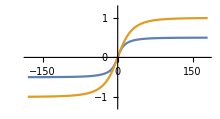

```mathematica
Plot[{f[ϕ Degree,0.5 fMax,α,α3]/Degree, f[ϕ Degree,fMax,α,α3]/Degree},{ϕ,-180,180},PlotRange->plotRange,ImageSize->imageSize,AxesStyle->axesStyle, AspectRatio->aspectRatio]
```

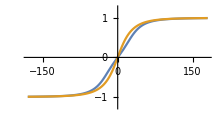

```mathematica
Plot[{ f[ϕ Degree,fMax,α/ 2,α3]/Degree, f[ϕ Degree,fMax,α,α3]/Degree},{ϕ,-180,180},PlotRange->plotRange,ImageSize->imageSize,AxesStyle->axesStyle, AspectRatio->aspectRatio]
```

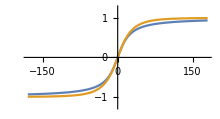

```mathematica
Plot[{ f[ϕ Degree,fMax,α,0]/Degree, f[ϕ Degree,fMax,α,α3]/Degree},{ϕ,-180,180},PlotRange->plotRange,ImageSize->imageSize,AxesStyle->axesStyle, AspectRatio->aspectRatio]
```

```mathematica
α = 0.1;
fMax = 1. Degree;
α3 = 1;
```

```mathematica
fσ[σ_,fmax_,α1_,α3_]:=ArcTan[(σ α1+α3 (σ)^3)/fmax π/2] 2/π fmax
```

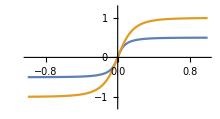

```mathematica
Plot[{fσ[ϕ,fMax/2,α ,α3]/Degree,fσ[ϕ ,fMax,α ,α3]/Degree},{ϕ,-1,1},PlotRange->{-plotRange[[2]],plotRange[[2]]},ImageSize->imageSize,AxesStyle->axesStyle, AspectRatio->aspectRatio]
```

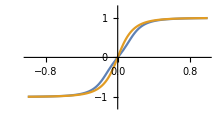

```mathematica
Plot[{fσ[ϕ,fMax,α/2,α3]/Degree,fσ[ϕ ,fMax,α,α3]/Degree},{ϕ,-1,1},PlotRange->{-plotRange[[2]],plotRange[[2]]},ImageSize->imageSize,AxesStyle->axesStyle, AspectRatio->aspectRatio]
```

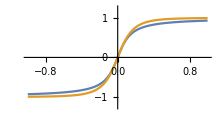

```mathematica
Plot[{fσ[ϕ,fMax,α ,0]/Degree,fσ[ϕ,fMax,α ,α3]/Degree},{ϕ,-1,1},PlotRange->{-plotRange[[2]],plotRange[[2]]},ImageSize->imageSize,AxesStyle->axesStyle, AspectRatio->aspectRatio]
```

```mathematica
Plot[{fσ[Tan[ϕ/4 Degree],fMax,α ,0]/Degree,fσ[ϕ,fMax,α ,α3]/Degree},{ϕ,-1,1},PlotRange->{-plotRange[[2]],plotRange[[2]]},ImageSize->imageSize,AxesStyle->axesStyle, AspectRatio->aspectRatio]
```

```mathematica
D[fσ[σ[t],FMAX,K1,K3],t]
```

(K1 σ'(t)+3 K3 (σ(t))^2 σ'(t))/((π^2 (K1 σ(t)+K3 (σ(t))^3)^2)/(4 FMAX^2)+1)

```mathematica
FullSimplify[%]
```

(σ'(t) (K1+3 K3 (σ(t))^2))/((π^2 (K1 σ(t)+K3 (σ(t))^3)^2)/(4 FMAX^2)+1)

```mathematica
D[f[σ[t],FMAX,K1,K3],t]
```

(K1 σ'(t)+3 K3 (σ(t))^2 σ'(t))/((π^2 (K1 σ(t)+K3 (σ(t))^3)^2)/(4 FMAX^2)+1)